```mathematica
μ=1;
ω=1.5;
σ=0.5;
p0=0;
n=100;
dt=10^-2;
tExact=100;
iter=tExact/dt;
x0=-5;
h=-2x0/n;
```

```mathematica
X[t_]=p0 t/μ
Σ2[t_]=σ*σ+t*t/(4μ*μ*σ*σ)
φ[x_,t_]=p0*(x-X[t])+p0*p0*t/(2μ)+t*(x-X[t])^2/(8*μ*σ*σ*Σ2[t])+Arg[1/Sqrt[μ+I*t/(2σ*σ)]]
exactψ[x_,t_]=(2π*Σ2[t])^(-1/4)*Exp[-(x-X[t])^2/(4*Σ2[t])+I*φ[x,t]]
ψ0[x_]=(2π*σ*σ)^(-1/4)*Exp[-x*x/(4σ*σ)+I*p0*x]
```

0

0.25+1. t^2

(0.5 t x^2)/(0.25+1. t^2)-1/2 Arg[1+(0.+2. ⅈ) t]

(ⅇ^(-x^2/(4 (0.25+1. t^2))+ⅈ ((0.5 t x^2)/(0.25+1. t^2)-1/2 Arg[1+(0.+2. ⅈ) t])))/((2 π)^(1/4) (0.25+1. t^2)^(1/4))

0.893244 ⅇ^(-1. x^2)

```mathematica
Manipulate[ReImPlot[exactψ[x,t],{x,-10,10}],{t,0,20}]
```

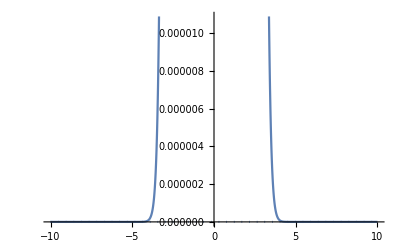

```mathematica
ReImPlot[ψ0[x],{x,-10,10}]
```

```mathematica
H=
z[x_]=(IdentityMatrix[n]-(I H dt)/2)psi
```